```mathematica
Clear[m,d,ϵ,u1,v1,v2,v3,v4,v5,v6,V,et,exp,n,g];
d[m_,ϵ_]:=m+3/(m+1)-ϵ;
bd[m_,ϵ_]:=(Gamma[(d[m,ϵ]-m+1)/2]Gamma[(d[m,ϵ]-m+1)/2])/(2^((2d[m,ϵ]+m-1)/2)π^((d[m,ϵ]-1)/2)Abs[Cos[((d[m,ϵ]-m+1)π)/2]]Gamma[(d[m,ϵ]-m)/2]Gamma[d[m,ϵ]-m+1]);
(*1/Sin[((m+1)π)/3]==(Gamma[(2-m)/3]Gamma[(1+m)/3])/π*)
u1[m_,ϵ_]:=If[m==2,1/(12 π^2),Gamma[(m+4)/(2(m+1))]/(2^(m-1)π^((m-2)/2)(4π)^(3/(2(m+1)))bd[m,ϵ]^((2-m)/2)(m+1)Gamma[m/2]Gamma[(2-m)/(2(m+1))])1/(Gamma[(2m+5)/(2(m+1))]Sin[(m+1)/3 π])];
v1[m_,ϵ_]:=Gamma[(m+1)/3]/bd[m,ϵ]^((2-m)/2);
v2[m_,ϵ_]:=2^(2-(2d[m,ϵ]-m/2))/(π^(d[m,ϵ]/2)Gamma[(d[m,ϵ]-m)/2]);(* I had earlier 2^(2+2d[m,ϵ]-m/2)/(π^(d[m,ϵ]/2)Gamma[(d[m,ϵ]-m)/2]) => typo and error *)
v3[m_,ϵ_]:=(2 EulerGamma)/(bd[m,ϵ]^((2-m)/2)(2π)^(3/(5-m)+m-2)Gamma[m/2]Gamma[3/(2(m+1))]π);
v4[m_,ϵ_]:= (6 EulerGamma)/(bd[m,ϵ]^((2-m)/2)(2π)^(3/(5-m)+m-2)Gamma[m/2]Gamma[3/(2(m+1))]π(m+1))-2/3;
v5[m_,ϵ_]:=(2^(5-2d[m,ϵ]+m/2) EulerGamma Gamma[(m+1)/3])/(bd[m,ϵ]^((2-m)/2)(π)^(d[m,ϵ]/2)Gamma[(d[m,ϵ]-m)/2]);
v6[m_,ϵ_]:=-(2^(5-2d[m,ϵ]+m/2) EulerGamma Gamma[(m+1)/3])/(bd[m,ϵ]^((2-m)/2)(π)^(d[m,ϵ]/2)Gamma[(d[m,ϵ]-m)/2]);

g[m_,d_]:=1-(2-m)/((m+1)(m+3/(m+1)-d));

eqn[m_,ϵ_,V_,et_,n_]:=-V (ϵ-(2-m)/(m+1)) +v2[m,ϵ] V^2+1/(6 (1+m) n)(-(-7+m^2) v1[m,ϵ]+V (v3[m,ϵ]-m^2 v3[m,ϵ]+2 v4[m,ϵ]+m (2+m) (2 v4[m,ϵ]+3 v5[m,ϵ]-v6[m,ϵ])+5 (-3 v5[m,ϵ]+v6[m,ϵ])+2 (1+m)^2 u1 [m,ϵ]))et;

etil[m_,ϵ_,n_]:=(n ϵ)/u1[m,ϵ];
```

### plot for m=1 -- 7a -- needs to be discarded

0.196575

{-13.8373,-0.594441}

{0.,-14.0074}

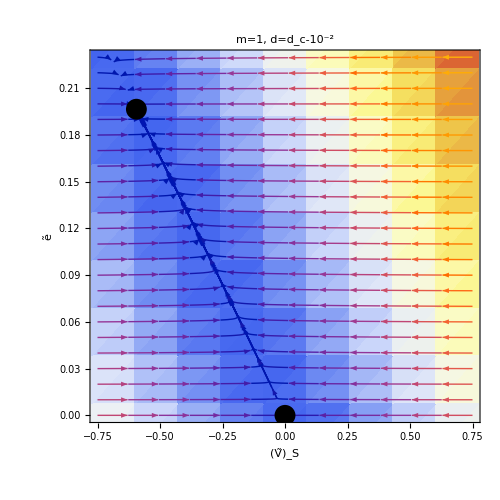

```mathematica
eps=10^-2;mm=1;NN=2;
etFP=etil[mm,eps,NN]//N
sol=SolveValues[eqn[mm,eps,Vt,NN/u1[mm,eps] eps,NN]==0,Vt]//N
SolveValues[eqn[mm,eps,Vt,0,NN]==0,Vt]//N
llim=0.0; dist=0.01; ulim=0.23;
ypoints=Range[llim,ulim,dist];
xpoints=ConstantArray[-0.75,Length[ypoints]];
points2=Transpose[{xpoints,ypoints}];

ypoints=Range[llim,ulim,dist];
xpoints=ConstantArray[0.75,Length[ypoints]];
points3=Transpose[{xpoints,ypoints}];
s=StreamDensityPlot[{-eqn[mm,eps,Vt,et,NN],et((mm+1)/3 eps -(mm+1)/(3NN)u1[mm,eps] et)},{Vt,-0.75,0.75},{et,llim,ulim},StreamPoints->{Join[(*points,*)points2,points3],Automatic,Scaled[2.5]},BaseStyle->Directive[Black,Bold,18,FontFamily->"Times"],(**)PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Bold,FontSize->18,FontFamily->"Times"]],Below](**),ColorFunction->"TemperatureMap",ImageSize->500,PlotLabel->Style["m=1, d=d_c-10^-2",Black,18],Frame->True,FrameLabel->{"(Ṽ)_S","ẽ"},FrameStyle->Directive[Black,Bold,22],FrameTicksStyle->Directive[Gray,Bold,18],ImagePadding->{{80, 40}, {80,5}}];

fp=Graphics[{PointSize[0.03],Black,Point[{(**){0,0},{sol[[2]],(* adding an offset for the sake of visualization *)etFP}(**)}]}];
s1=Show[s,fp]
SetDirectory[NotebookDirectory[]];
Export["flow1.jpg",Rasterize[s1,ImageResolution-> 500],ImageSize->500];
```

### plot for m=1, d=2

```mathematica
lim=0.1;eps=0.5;mm=1;NN=2;
etil[mm,eps,NN]
Solve[eqn[mm,eps,Vt,NN/u1[mm,eps] eps,NN]==0,Vt]
Solve[eqn[mm,eps,Vt,0,NN]==0,Vt]
```

11.9886

{{Vt→8.27989},{Vt→27.3662}}

{{Vt→0.},{Vt→0.}}

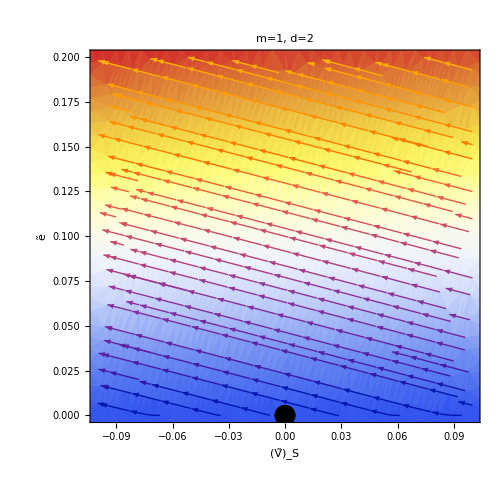

```mathematica
fp=Graphics[{PointSize[0.03],Black,Point[{{0,0},{0,0}(**)}]}];s=StreamDensityPlot[{-eqn[mm,eps,Vt,et,NN],et((mm+1)/3 eps -(mm+1)/(3NN)u1[mm,eps] et)},{Vt,-lim,lim},{et,0,2lim},BaseStyle->Directive[Black,Bold,18,FontFamily->"Times"],(**)PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Bold,FontSize->18,FontFamily->"Times"]],Below](**),ColorFunction->"TemperatureMap",ImageSize->500,PlotLabel->Style["m=1, d=2",Black,18],Frame->True,FrameLabel->{"(Ṽ)_S","ẽ"},FrameStyle->Directive[Black,Bold,22],FrameTicksStyle->Directive[Gray,Bold,18],ImagePadding->{{80, 40}, {80,5}}];
s1=Show[s,fp,ImagePadding->{{80, 40}, {80,5}}]

SetDirectory[NotebookDirectory[]];
Export["flow2.jpg",Rasterize[s1,ImageResolution-> 500],ImageSize->500];
```

{-1.60236,-0.834367}

{-4.32786,0.}

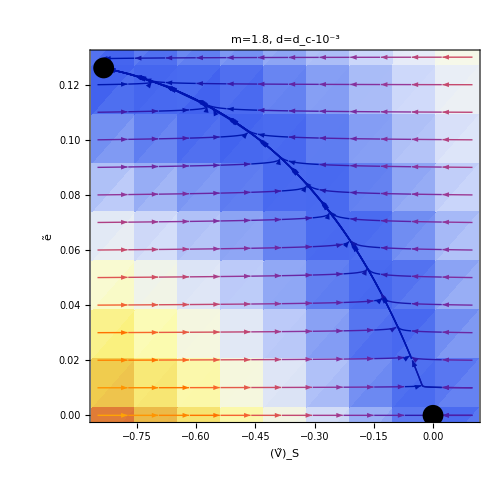

```mathematica
eps=10^-3;mm=1.8;NN=2;etFP=etil[mm,eps,NN];
sol=SolveValues[eqn[mm,eps,Vt,NN/u1[mm,eps] eps,NN]==0,Vt]
SolveValues[eqn[mm,eps,Vt,0,NN]==0,Vt]
fp=Graphics[{PointSize[0.03],Black,Point[{{0,0},{sol[[2]],etFP}(**)}]}];

llim=(*0.01*)0; ulim=0.13;
ypoints=Range[llim,ulim,0.01];
xpoints=ConstantArray[0.1,Length[ypoints]];
points=Transpose[{xpoints,ypoints}];

ypoints=Range[llim,ulim,0.01];
xpoints=ConstantArray[-0.85,Length[ypoints]];
points2=Transpose[{xpoints,ypoints}];

ypoints=Range[llim,0.01,0.01];
xpoints=ConstantArray[0.1,Length[ypoints]];
points3=Transpose[{xpoints,ypoints}];
s=StreamDensityPlot[{-eqn[mm,eps,Vt,et,NN],et((mm+1)/3 eps -(mm+1)/(3NN)u1[mm,eps] et)},{Vt,-0.85,0.1},{et,llim,ulim},StreamPoints->{Join[points,points2,points3],Automatic,Scaled[1.5]},BaseStyle->Directive[Black,Bold,18,FontFamily->"Times"],(**)PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Bold,FontSize->18,FontFamily->"LM Roman 10"]],Below](**),ColorFunction->"TemperatureMap",ImageSize->500,PlotLabel->Style["m=1.8, d=d_c-10^-3",Black,18],Frame->True,FrameLabel->{"(Ṽ)_S","ẽ"},FrameStyle->Directive[Black,Bold,22],FrameTicksStyle->Directive[Gray,Bold,18],ImagePadding->{{80, 40}, {80,5}}];

s1=Show[s,fp,ImagePadding->{{80, 40}, {80,5}}]
SetDirectory[NotebookDirectory[]];
Export["flow3.jpg",Rasterize[s1,ImageResolution-> 500],ImageSize->500];
```

### plot for m=2

```mathematica
lim=0.1;del=lim/100;eps=0;mm=2;NN=2;
etil[mm,eps,NN]
Solve[eqn[mm,eps,Vt,NN/u1[mm,eps] eps,NN]==0,Vt]
Solve[eqn[mm,eps,Vt,0,NN]==0,Vt]
```

0

{{Vt→0},{Vt→0}}

{{Vt→0},{Vt→0}}

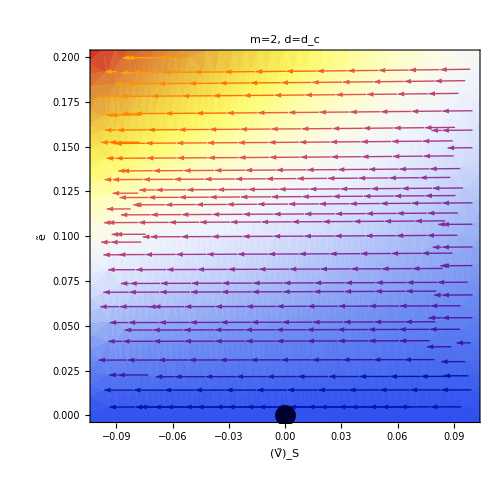

```mathematica
fp=Graphics[{PointSize[0.03],Darker[Blend[{Blue,Black},{0.3,0.7}]],Point[{{0,0}}]}];

s=StreamDensityPlot[{-eqn[mm,eps,Vt,et,NN],et((mm+1)/3 eps -(mm+1)/(3NN)u1[mm,eps] et)},{Vt,-lim,lim},{et,0.0,0.2},BaseStyle->Directive[Black,Bold,18,FontFamily->"Times"],(**)PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[Bold,FontSize->18,FontFamily->"Times"]],Below](**),ColorFunction->"TemperatureMap",ImageSize->500,PlotLabel->Style["m=2, d=d_c",Black,18],Frame->True,FrameLabel->{"(Ṽ)_S","ẽ"},FrameStyle->Directive[Black,Bold,22],FrameTicksStyle->Directive[Gray,Bold,18]];

s1=Show[s,fp,ImagePadding->{{80, 40}, {80,5}}]
SetDirectory[NotebookDirectory[]];
Export["flow4.jpg",Rasterize[s1,ImageResolution-> 500],ImageSize->500];
```